```mathematica
g=({{1}, {0}});e=({{0}, {1}});gg=KroneckerProduct[g,g];ee=KroneckerProduct[e,e];ψ=ⅈ Exp[-(ⅈ J t)/4](Sin[(J t)/4]ee+ⅈ Cos[(J t)/4]gg)
conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj;
```

{{-ⅇ^(-1/4 ⅈ J t) Cos[(J t)/4]},{0},{0},{ⅈ ⅇ^(-1/4 ⅈ J t) Sin[(J t)/4]}}

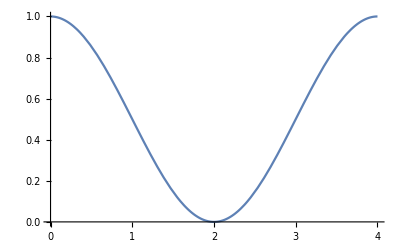

```mathematica
Plot[ComplexExpand[Abs[(hc[gg].ψ)[[1,1]]]^2//.J->π]//FullSimplify,{t,0,4}]
```

```mathematica
HJ=J/8 (KroneckerProduct[σp,σm]+KroneckerProduct[σm,σp]);
```

```mathematica
MatrixExp[-ⅈ HJ t].gg
```

{{1},{0},{0},{0}}

```mathematica
Hpulse[vec_]:=1/2 Ω ∑_(n=1)^3 σ⟦n⟧ Normalize[vec]⟦n⟧
```

```mathematica
pulse=KroneckerProduct[Hpulse[{1,0,0}],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],Hpulse[{1,0,0}]]
```

{{0,Ω/2,Ω/2,0},{Ω/2,0,0,Ω/2},{Ω/2,0,0,Ω/2},{0,Ω/2,Ω/2,0}}

```mathematica
FullSimplify[MatrixExp[-ⅈ pulse π/(2Ω)].MatrixExp[-ⅈ HJ t].MatrixExp[-ⅈ pulse π/(2Ω)].gg]
```

{{1/2-1/2 ⅇ^(-1/2 ⅈ J t)},{0},{0},{-1/2-1/2 ⅇ^(-1/2 ⅈ J t)}}

```mathematica
TrueQ[ⅈ Exp[-(ⅈ J t)/4]Sin[(J t)/4]==1/2-1/2 ⅇ^(-1/2 ⅈ J t)]
TrueQ[ⅈ Exp[-(ⅈ J t)/4]ⅈ Cos[(J t)/4]==-1/2-1/2 ⅇ^(-1/2 ⅈ J t)]
```

False

False

```mathematica
FullSimplify[ⅈ Exp[-(ⅈ J t)/4]Sin[(J t)/4]-(1/2-1/2 ⅇ^(-1/2 ⅈ J t))]
```

0

```mathematica
FullSimplify[ⅈ Exp[-(ⅈ J t)/4]ⅈ Cos[(J t)/4]-(-1/2-1/2 ⅇ^(-1/2 ⅈ J t))]
```

0